Loop invariant:

	In computer science, a loop invariant is a property of a program loop that is true before (and after) each iteration. It is a logical assertion, sometimes checked within the code by an assertion call. Knowing its invariant(s) is essential in understanding the effect of a loop.

Insertion Sort

Java

```mathematica
public class InsertionSort{
	
	public static void insertionSortSmallToLarge(int[] arr){
		
		for(int i = 1; i < arr.length; i++){
		
			int pivot = arr[i];
			int j = i - 1;
			while(j >= 0 && arr[j] > pivot){
				arr[j+1] = arr[j];
				j--;
			}
			arr[j+1] = pivot;
			
		}
		
	}
	
	public static void insertionSortLargeToSmall(int[] arr){
		
		for(int i = 1; i < arr.length; i++){
		
			int pivot = arr[i];
			int j = i - 1;
			while(j >= 0 && arr[j] < pivot){
				arr[j+1] = arr[j];
				j--;
			}
			arr[j+1] = pivot;
			
		}
		
	}
	
}
```

C

```mathematica
int insertion_sort_small_to_large(int arr[])
{
	
}

int insertion_sort_large_to_small(int arr[])
{
	
}
```

Python

```mathematica
def insertion_sort_small_to_large(int arr[]){
	
}

def insertion_sort_large_to_small(int arr[]){
	
}
```

Random - access machine (RAM) :
	In computer science, random-access machine (RAM) is an abstract machine in the general class of register machines. The RAM is very similar to the counter machine but with the added capability of ‘indirect addressing’ of its registers. Like the counter machine the RAM has its instructions in the finite-state portion of the machine (the so-called Harvard architecture).
	The RAM’s equivalent of the universal Turing machine – with its program in the registers as well as its data.

Merge Sort

Java

```mathematica
public class MergeSort{
	
	public static void mergeSortSmallToLarge(int[] arr){
		
		MergeSort.sortSmallToLarge(arr, 0, arr.length - 1);
		
	}
	
	public static void sortSmallToLarge(int[] arr, int start, int end){
		
		if(start < end){
		
			mid = (end + start) / 2;
			sortSmallToLarge(arr, start, mid);
			sortSmallToLarge(arr, mid + 1, end);
			mergeSmallToLarge(arr, start, mid, end);
		
		}
		
	}
	
	public static void mergeSmallToLarge(int[] arr, int start, int mid, int end){
		
		int[] temp = arr[];
		int i = start;
		int j = mid + 1;
		int count = 0;
		while(i < mid + 1 && j < end){
			
			if(temp[i] < temp[j]){
				arr[count] = temp[i];
				i++;
			}
			
			if(temp[i] >= temp[j]){
				arr[count] = temp[j];
				j++;
			}
			
			count++;
		
		}
		
		while(i < mid + 1){
			arr[count] = temp[i];
			i++;
			count++;
		}
		
		while(j < end){
			arr[count] = temp[j];
			j++;
			count++;
		}
		
	}
	
	public static void mergeSortLargeToSmall(int[] arr){
		
		
		
	}
	
}
```

```mathematica
Plot[n*Log[2, n]+n, {n, 0, 30}]
```

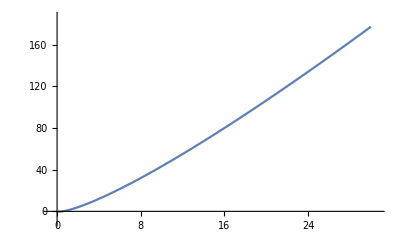

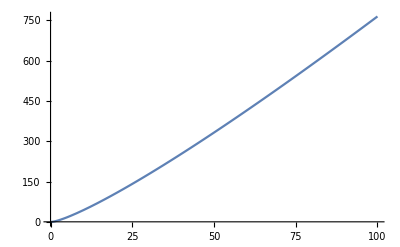

```mathematica
Plot[n*Log[2, n]+n, {n, 0, 100}]
```